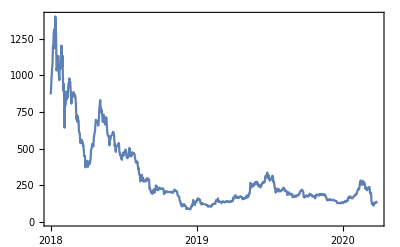

135.884

```mathematica
pricesFull=FinancialData["ETH/USD",{2018}];
DateListPlot[%]
prices=pricesFull["Values"] ;

Import["https://api.coingecko.com/api/v3/coins/ethereum/market_chart?vs_currency=usd&days=815","json"];
First[%][[2]];
prices=Transpose[%][[2]];

Last[%]
```

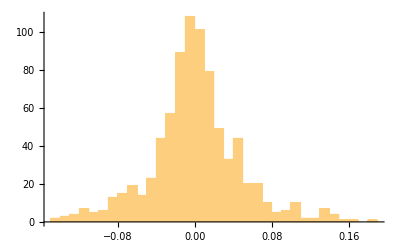

```mathematica
logReturnF:=(Log[Last[#]/First[#]])&;
logReturns = logReturnF/@Partition[prices,2,1];
Histogram[%,100]
```

```mathematica
σimp=StandardDeviation[logReturns];
Print["σ: ",%];
Mean[logReturns];
Print["Mean(Returns): ",%];
Mean[logReturns]-(1/2)*(σimp)^2;
Print["μ (wrong?): ",%];
μimp=Mean[logReturns]+(1/2)*(σimp)^2;
Print["μ: ",%];
FindProcessParameters[prices,GeometricBrownianMotionProcess[μ,σ,s0]]
```

σ: 0.0541016

Mean(Returns): -0.00240284

μ (wrong?): -0.00386633

μ: -0.000939344

{μ→-0.000939344,σ→0.0541016,s0→963.056}